```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
xmin=-12;
ymin=-12;
legendpos={0.5,0.1};
labelpos={0.5,0.9};
energycolor[z_]:=Blend[{White,White,White,RGBColor[0.6392156862745098,0.45098039215686275,0.3176470588235294],RGBColor[0.23137254901960785,0.1607843137254902,0.11372549019607843]},z];
baryoncolor[z_]:=Blend[{RGBColor[0.,0.5764705882352941,0.5764705882352941],White,RGBColor[0.9568627450980393,0.47843137254901963,0.]},z];
strangecolor[z_]:=Blend[{RGBColor[0.5019607843137255,0.,1.],White,RGBColor[0.,0.5019607843137255,0.]},z];
chargecolor[z_]:=Blend[{Blue,White,Red},z];
```

```mathematica
MakePlot[inEN_,inNB_,inNS_,inNQ_,legpos_,labpos_,ShowOutput_]:=Module[{myENplot,myNBplot,myNSplot,myNQplot,myplot},

myENplot=
MatrixPlot[
Transpose@inEN,
DataReversed->True,
ColorFunction->(energycolor[#]&),
PlotRange->All,
ImageSize->500,
MaxPlotPoints->1000000,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,16]],Scaled[legpos]],
FrameLabel->{{None,Style["",Bold,20,Black]},{Style["y (fm)",Bold,20,Black],None}},
FrameTicksStyle->
{{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]},
{Directive[FontOpacity->0,FontSize->0],
Directive[Black,20]}},
ImagePadding->{{All,0},{0,All}},
Epilog->{
Text[Style["Energy Density (GeV / fm^3)",Bold,24,Black],Scaled[labpos]]
}
];

myNBplot=
MatrixPlot[
Transpose@inNB,
DataReversed->True,
ColorFunction->(baryoncolor[#]&),
PlotRange->All,
ImageSize->500,
MaxPlotPoints->1000000,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,16]],Scaled[legpos]],
LabelStyle->Directive[Black,14],
FrameLabel->{{None,Style["",Bold,20,Black]},{None,Style["",Bold,20,Black]}},
FrameTicksStyle->
{{Directive[FontOpacity->0,FontSize->0],
Directive[Black,20]},
{Directive[FontOpacity->0,FontSize->0],
Directive[Black,20]}},
ImagePadding->{{0,All},{0,All}},
Epilog->{
Text[Style["Baryon Density (fm^-3)",Bold,24,Black],Scaled[labpos]]
}
];

myNSplot=
MatrixPlot[
Transpose@inNS,
DataReversed->True,
ColorFunction->(strangecolor[#]&),
PlotRange->All,
ImageSize->500,
MaxPlotPoints->1000000,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,16]],Scaled[legpos]],
LabelStyle->Directive[Black,14],
FrameLabel->{{Style["x (fm)",Bold,20,Black],None},{Style["y (fm)",Bold,20,Black],None}},
FrameTicksStyle->
{{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]
},
{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]}},
ImagePadding->{{All,0},{All,0}},
Epilog->{
Text[Style["Strangeness Density (fm^-3)",Bold,24,Black],Scaled[labpos]]
}
];

myNQplot=
MatrixPlot[
Transpose@inNQ,
DataReversed->True,
ColorFunction->(chargecolor[#]&),
PlotRange->All,
ImageSize->500,
MaxPlotPoints->1000000,
DataRange->{{xmin,-xmin},{ymin,-ymin}},
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendLayout->"Row",LabelStyle->Directive[Black,16]],Scaled[legpos]],
LabelStyle->Directive[Black,14],
FrameLabel->{{Style["x (fm)",Bold,20,Black],None},{None,Style["",Bold,16,Black]}},
FrameTicksStyle->
{{Directive[FontOpacity->0,FontSize->0],
Directive[Black,20]
},
{Directive[Black,20],
Directive[FontOpacity->0,FontSize->0]}},
ImagePadding->{{0,All},{All,0}},
Epilog->{
Text[Style["Charge Density (fm^-3)",Bold,24,Black],Scaled[labpos]]
}
];

myplot=
GraphicsGrid[{{
myENplot,
myNBplot
},{
myNSplot,
myNQplot
}},ImageSize->1000,Spacings->0,Alignment->{{Right,Left},{Bottom,Top}}];

If[ShowOutput,
Print[myplot];
];

Return[myplot];

]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DensityData= Import["densities0.dat"][[2;;]];
```

```mathematica
imax=Round@Abs[2*12/0.06];
jmax=Round@Abs[2*12/0.06];
```

```mathematica
EnergyData=SparseArray[Map[{Round[(#_⟦1⟧-12)/0.06],Round[(#_⟦2⟧-12)/0.06]}->#_⟦3⟧&,DensityData],{imax,jmax}];
```

```mathematica
BaryonData=SparseArray[Map[{Round[(#_⟦1⟧-12)/0.06],Round[(#_⟦2⟧-12)/0.06]}->#_⟦4⟧&,DensityData],{imax,jmax}];
```

```mathematica
StrangeData=SparseArray[Map[{Round[(#_⟦1⟧-12)/0.06],Round[(#_⟦2⟧-12)/0.06]}->#_⟦5⟧&,DensityData],{imax,jmax}];
```

```mathematica
ChargeData=SparseArray[Map[{Round[(#_⟦1⟧-12)/0.06],Round[(#_⟦2⟧-12)/0.06]}->#_⟦6⟧&,DensityData],{imax,jmax}];
```

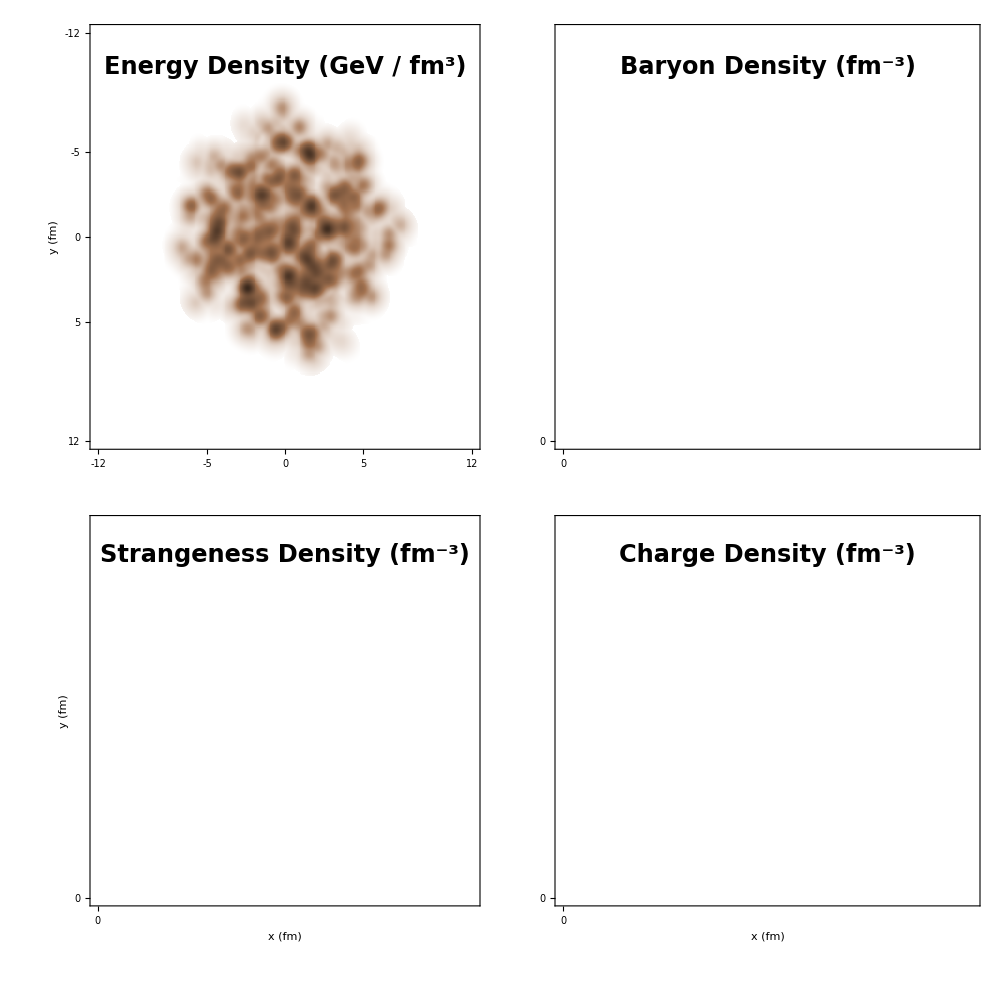

```mathematica
AllDensityPlots=MakePlot[EnergyData,BaryonData,StrangeData,ChargeData,legendpos,labelpos,False]
```